# Load packages

```mathematica
SetDirectory[NotebookDirectory[]<>"../../package/"];
Get["funcs_rxns_moms.m"]
```

# Make graphs & Export

## Import data description

```mathematica
volExp=14;
cdir="../../"<>getCacheDirRaw[volExp];
dataDesc=importDataDesc[cdir<>"data_desc.txt"];

nv=3;
nh=1;
```

## Freqs

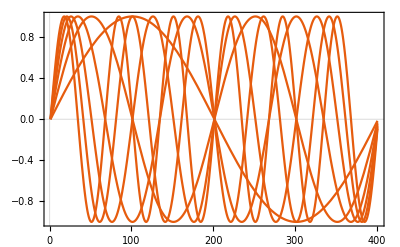

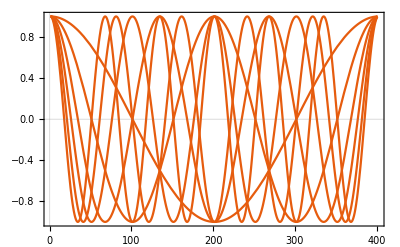

```mathematica
freqs={1,2,3,4,5,6}//N;
freqs=2*Pi/dataDesc["noTpts"]*freqs;
Plot[Table[Sin[freq*(t-1)],{freq,freqs}],{t,1,dataDesc["noTpts"]}]
Plot[Table[Cos[freq*(t-1)],{freq,freqs}],{t,1,dataDesc["noTpts"]}]
```

## Input graph without standardization

```mathematica
muhCosCoeffsInit=ConstantArray[0,Length[freqs]];
muhSinCoeffsInit=ConstantArray[0,Length[freqs]];
varhCosCoeffsInit=ConstantArray[0,Length[freqs]];
varhSinCoeffsInit=ConstantArray[0,Length[freqs]];
```

## Make graph

```mathematica
graphInputsWOSTD=makeGraphInputsWOSTD[nv,nh,freqs,muhCosCoeffsInit,muhSinCoeffsInit,varhCosCoeffsInit,varhSinCoeffsInit];
```

## Export

```mathematica
SetDirectory[NotebookDirectory[]];
createDirIfNeeded["training_data"];
Export["training_data/graph_params_inputs_wo_std.wlnet",graphInputsWOSTD]
```

training_data_params/graph_inputs_wo_std.wlnet

## Graph for calculating STDs

```mathematica
fourier[offset_,sinCoeffs_,cosCoeffs_,freqs_,tptPlt_]:=Module[
{range,pts}
,
range=Max[Total[Abs[sinCoeffs]+Abs[cosCoeffs]]+10^-8,1];
pts=Table[offset[[1]]+(Sum[sinCoeffs[[i]]*Sin[freqs[[i]]*(tpt-1)]+cosCoeffs[[i]]*Cos[freqs[[i]]*(tpt-1)],{i,Length[freqs]}])/range,{tpt,tptPlt}];

Return[pts];
];
```

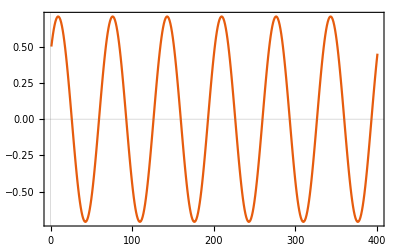
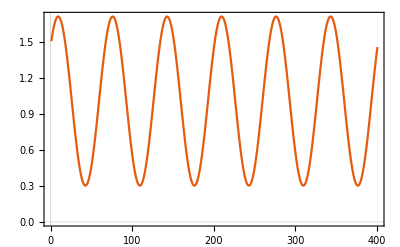

```mathematica
(* Highest freq sin + cos only *)
freqsTrial={freqs[[-1]]};
muhCosCoeffsInitTrial={1.0};
muhSinCoeffsInitTrial={1.0};
varhCosCoeffsInitTrial={1.0};
varhSinCoeffsInitTrial={1.0};

tptsTrial=Table[t,{t,1,dataDesc["noTpts"]}];
muhTrial=fourier[{0.0},muhSinCoeffsInitTrial,muhCosCoeffsInitTrial,freqsTrial,tptsTrial];
varhTrial=fourier[{1.01},varhSinCoeffsInitTrial,varhCosCoeffsInitTrial,freqsTrial,tptsTrial];

Row[{
ListLinePlot[Flatten[muhTrial]],
ListLinePlot[Flatten[varhTrial]]
}]
```

## Make graph

```mathematica
graphCalculateSTDs=makeGraphInputsWOSTD[nv,nh,freqsTrial,muhCosCoeffsInitTrial,muhSinCoeffsInitTrial,varhCosCoeffsInitTrial,varhSinCoeffsInitTrial];
```

## Export

```mathematica
SetDirectory[NotebookDirectory[]];
Export["training_data/graph_params_calculate_stds.wlnet",graphCalculateSTDs]
```

training_data_params/graph_calculate_stds.wlnet